```mathematica
SetDirectory[NotebookDirectory[]]
Get["eigenfaces-algorithm.m"]
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
```

/home/nathan/QEA-Eigenfaces/Eigenfaces

```mathematica
(*clustAll gives the total tour distance between the projected images of each person. *)
clusterAll[eigenfaces_,images_,numTrainingIndividuals_]:=Module[{components},
components=Map[eigenCompress[#1,eigenfaces[[All]],All]&,images];
components=Partition[components,8];
components=MapThread[Labeled[#1,#2]&,{components,names}];
Return[Transpose[{Map[FindShortestTour,components[[1;;numTrainingIndividuals,1]]][[All,1]],components[[1;;numTrainingIndividuals,2]]}]]]
```

```mathematica
{eigenvalues43,eigenfaces43}=findEigenfaces[Map[#-Mean[#]&, Flatten/@images[[1;;344;;8]]]];
```

```mathematica
Length[eigenfaces43]
components43=Map[eigenCompress[#1,eigenfaces43[[2;;3]],All]&,images];
components43=Partition[components43,8];
components43=MapThread[Labeled[#1,#2]&,{components43,names}];
```

43

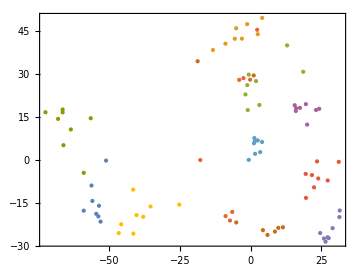
-Graphics--Graphics--Graphics-

```mathematica
Labeled[
ListPlot[components43[[3;;13]],PlotStyle->PointSize[Large],ImageSize->Medium,AspectRatio->Automatic,Ticks->None ,Axes->None,FrameTicksStyle->Directive[FontColor->White,FontSize->1], Frame->{{True,None},{True,None}}],

Rasterize/@{"EF2","EF3"},{Bottom,Left},RotateLabel->True]
```

```mathematica
-Graphics--Graphics--Graphics-
```

-Graphics--Graphics--Graphics-

```mathematica
components3=Map[eigenCompress[#1,eigenfaces[[1;;3]],All]&,images];
components3=Partition[components3,8];
(*components3=MapThread[Labeled[#1,#2]&,{components3,names}];*)
ListPointPlot3D[components3[[All]],PlotStyle->PointSize[Large],ImageSize->Large]
```

-Graphics3D-

301

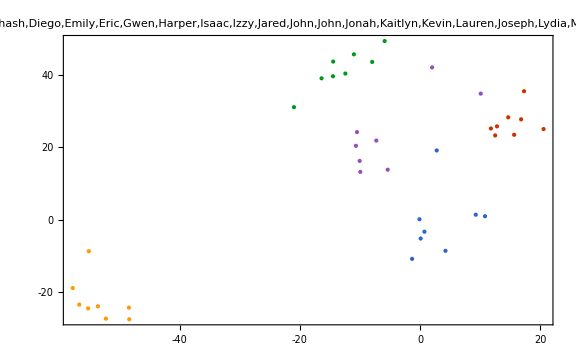

```mathematica
{eigenvalues301,eigenfaces301}=findEigenfaces[Map[#-Mean[#]&, Flatten/@images[[Complement[Range[344],Range[2,344,8]]]]]];
Length[eigenfaces301]
components301=Map[eigenCompress[#1,eigenfaces301[[2;;3]],All]&,images];
components301=Partition[components301,8];
components301=MapThread[Labeled[#1,#2]&,{components301,names}];
ListPlot[components301[[1;;5]],PlotStyle->PointSize[Large],ImageSize->Large,PlotLabel->names,PlotTheme->"Web"]
```

```mathematica
Dimensions@eigenfaces301[[1;;43,All]]
```

{43,92160}

```mathematica
Mean[clusterAll[eigenfaces43,images,43][[All,1]]]
Mean[clusterAll[eigenfaces301[[1;;43,All]],images,43][[All,1]]]
```

172.968

200.516

```mathematica
{eigenvaluesDisgusted,eigenfacesDisgusted}=findEigenfaces[Map[#-Mean[#]&, Flatten/@images[[Complement[Range[344],Range[7,344,8]]]]]];
Mean[clusterAll[eigenfacesDisgusted[[1;;43,All]],images,43][[All,1]]]
```

199.04

```mathematica
Grid[Transpose@{{"Training Size","43","301"},{"Clustering Coefficient",173,201}}]
```

Training Size | Clustering Coefficient
43 | 173
301 | 201

```mathematica
Labeled[
ListPlot[components43[[3;;13]],PlotStyle->PointSize[Large],ImageSize->Medium,AspectRatio->Automatic,Ticks->None ,Axes->None,FrameTicksStyle->Directive[FontColor->White,FontSize->1], Frame->{{True,None},{True,None}}],

Rasterize/@{"EF2","EF3"},{Bottom,Left},RotateLabel->True]
```

-Graphics--Graphics--Graphics-

```mathematica
Length[eigenfaces43]
components43=Map[eigenCompress[#1,eigenfaces43[[2;;3]],All]&,images];
components43=MapThread[PopupWindow,{components43,Map[Image,images]}];
components43=Partition[components43,8];
Dimensions[components43]
components43=MapThread[Labeled[#1,#2]&,{components43,names}];
```

43

{43,8}

```mathematica
Dimensions[components43]
components43
```

{43}

{{{22.4251,29.0965},{21.1941,28.7698},{21.3621,24.3161},{28.5264,22.6229},{24.0174,23.1908},{24.1682,29.5826},{26.5585,33.9667},{25.18,25.6884}}Ariana,{{5.81735,-0.398715},{2.94577,-5.08037},{5.22231,6.06421},{13.4301,5.76589},{8.52955,-4.22128},{5.83973,1.91009},{9.96984,20.3857},{16.413,3.78257}}Bryan,{{-58.9772,-17.6542},{-54.5475,-18.7623},{-53.026,-21.4645},{-53.7887,-19.6605},{-53.5856,-15.9453},{-55.9128,-14.2617},{-56.2176,-8.89544},{-51.0738,-0.217384}}Charlie,{{-13.308,38.2971},{-1.1915,47.3262},{2.53542,43.8152},{4.10328,49.4776},{-5.09243,45.8774},{-3.05797,42.2655},{-8.87331,40.5144},{-5.58719,42.2151}}Chloe,{{-0.667076,29.7171},{-1.16438,26.0684},{1.92725,27.4802},{3.11147,19.1506},{-0.984672,17.3695},{-1.81017,22.8302},{18.6101,30.7163},{12.9245,39.91}}Chris,{{-8.83768,-19.5472},{-7.26954,-21.0931},{-6.48559,-18.0961},{-17.7555,-0.0196138},{-4.02243,27.8942},{-2.50694,28.5074},{-0.161025,27.9679},{2.33528,45.3495}}Danny,{{24.6035,-25.448},{25.9163,-27.3513},{27.2259,-26.9284},{31.5116,-17.6042},{31.3984,-19.8869},{28.9959,-23.7563},{26.5116,-28.4543},{27.619,-27.2223}}David,{{4.36717,-24.447},{5.98489,-26.0984},{11.4457,-23.4477},{9.80992,-23.6335},{8.606,-24.934},{-5.0482,-21.7672},{1.11225,29.4399},{-18.7085,34.3886}}Dhash,{{3.38908,2.73884},{1.60479,2.1463},{-0.646231,0.0357314},{2.56096,6.835},{1.51764,6.48207},{4.05129,6.25895},{1.19792,5.81732},{1.33298,7.63014}}Diego,{{-41.5034,-10.3358},{-41.4333,-25.648},{-46.6134,-25.4663},{-45.736,-22.4071},{-35.3577,-16.2047},{-25.1874,-15.5572},{-37.9435,-19.8105},{-40.3252,-19.2002}}Emily,{{15.5847,19.0711},{16.0931,18.0481},{17.4401,18.1521},{24.2704,17.8268},{19.5397,19.4536},{23.1403,17.4248},{15.9956,17.0573},{19.9985,12.3259}}Eric,{{-72.4947,16.6256},{-66.4248,17.5963},{-68.0411,14.3077},{-56.5025,14.5387},{-66.4434,16.5796},{-63.5255,10.63},{-58.9771,-4.48209},{-66.1463,5.13921}}Gwen,{{23.5026,-0.502954},{19.4849,-4.85419},{21.7011,-5.2613},{31.1801,-0.66278},{27.2633,-7.13649},{23.9115,-6.43598},{19.5839,-13.2074},{22.4269,-9.53139}}Harper,{{-8.7936,-14.9522},{-7.78328,-15.0737},{-8.3184,-15.6506},{-14.9482,-27.9686},{-11.8112,-22.1504},{-5.91956,-8.46914},{-0.628902,-14.3441},{-1.07828,-10.0052}}Isaac,{{-46.695,-28.0332},{-45.7391,-28.5532},{-48.7891,-29.0184},{-45.7302,-27.7184},{-44.1361,-26.9115},{-43.2671,-27.7975},{-44.0771,-30.2159},{-42.9803,-25.2824}}Izzy,{{9.37998,-11.3229},{9.12152,-12.9792},{5.25732,-5.03669},{2.52062,-5.28475},{4.3257,-6.84181},{4.4336,-5.13689},{2.54089,-7.23494},{2.00708,1.36956}}Jared,{{3.99979,-9.93325},{4.76921,-9.96379},{5.33844,-10.1048},{8.28183,-6.14313},{3.23373,-12.0008},{2.58897,-5.73048},{14.4663,5.09293},{3.41353,-12.5375}}John,{{21.4452,-24.1243},{22.9828,-22.8764},{24.0462,-21.5501},{22.485,-22.5842},{22.3087,-20.4098},{21.9326,-20.8406},{21.4596,-18.0588},{22.6604,-18.7985}}John,{{5.42467,33.8998},{5.05281,30.0765},{5.45122,29.3999},{8.73024,33.4222},{6.53281,28.8456},{8.20071,31.8901},{10.9781,37.2773},{11.9586,40.7924}}Jonah,{{-59.6193,28.0456},{-60.0777,27.7777},{-59.8494,27.6382},{-53.0481,34.9568},{-57.7574,36.393},{-58.8855,37.3505},{-53.2784,33.391},{-53.1256,47.5536}}Kaitlyn,{{11.2709,-11.3037},{11.1329,-11.8969},{21.2777,-13.2346},{18.7964,-10.4008},{16.4132,-11.0912},{18.6658,-10.2271},{23.3943,-7.7397},{23.1602,-6.41326}}Kevin,{{-61.0298,-17.536},{-61.6086,-13.7412},{-59.2002,-12.878},{-64.203,-14.4095},{-64.9639,-18.2427},{-60.847,-16.8919},{-61.943,-21.8564},{-64.1529,-13.6832}}Lauren,{{7.35331,-13.248},{8.72522,-16.532},{7.41022,-18.175},{15.3804,-8.4395},{11.2929,-32.4694},{9.59188,-27.9325},{14.9227,-26.6245},{9.53244,-26.0889}}Joseph,{{-72.1029,-25.5407},{-67.8208,-25.9345},{-62.6146,-19.8529},{-56.4071,-20.1765},{-62.5367,-21.7651},{-55.1588,-9.95354},{-54.6,-15.8995},{-60.259,-4.02011}}Lydia,{{11.6132,-39.9582},{9.17629,-45.5266},{9.82291,-43.8045},{15.3068,-35.8985},{13.6791,-42.1331},{14.5243,-39.1553},{22.464,-24.177},{15.9046,-39.4916}}Margo,{{4.25226,-11.4332},{5.93075,-12.2111},{9.3734,-12.2857},{6.75507,-10.6005},{10.0986,-11.0388},{12.1312,-9.29331},{11.357,-14.3928},{13.1894,-17.7322}}Mark,{{-70.862,4.72723},{-70.4995,4.71678},{-66.6469,7.30988},{-66.2042,17.7812},{-61.9531,32.1542},{-53.7396,36.1983},{-60.4146,35.4056},{-47.9515,37.6332}}Mary,{{5.34656,1.29854},{4.50608,-3.07752},{7.39635,-2.67918},{5.03057,-9.35133},{4.81961,6.88407},{7.22667,7.02806},{4.69749,12.3943},{6.94339,11.1116}}Max,{{-71.0731,14.6326},{-65.6474,3.36321},{-69.4329,4.00421},{-69.6289,19.2641},{-68.8726,15.0767},{-65.8256,14.6328},{-68.7702,16.0007},{-67.8773,16.2012}}Mica,{{33.5552,57.7582},{33.5691,57.5088},{31.5727,56.1532},{32.533,56.403},{28.0111,55.7842},{28.055,54.7031},{22.8371,51.6484},{24.9713,51.8097}}Nathan,{{-11.1015,38.1661},{-10.3976,36.9581},{-10.1533,36.1607},{-7.46859,37.9563},{-7.06219,37.091},{-5.08447,37.0902},{-8.26384,33.6235},{-10.2538,29.7534}}Paige,{{-7.69922,-12.4333},{-6.86418,-12.8528},{-6.9451,-12.9048},{-8.21139,-12.003},{-6.54368,-10.4608},{-6.42941,-14.8357},{-3.86387,-13.5403},{-4.4134,-9.78932}}Rebecca,{{-54.769,22.6143},{-51.9599,22.7157},{-50.7149,24.7377},{-52.1256,25.06},{-51.7206,19.1115},{-51.115,22.2953},{-45.5624,25.6151},{-44.4763,24.7353}}Regina,{{6.93751,-23.0716},{8.5486,-24.0618},{10.1145,-24.1997},{9.69141,-22.0612},{8.11626,-19.9717},{10.0645,-25.114},{8.29514,-21.4318},{8.51732,-21.2535}}Ruby,{{9.0356,-31.2693},{9.91191,-26.2638},{17.643,-26.8907},{9.65934,-27.9737},{11.2937,-22.7238},{12.95,-18.439},{17.2502,-27.4943},{19.5347,-27.2818}}Sam,{{-47.2008,26.5076},{-48.9946,20.2729},{-43.7836,19.2688},{-46.4116,25.4169},{-47.8062,22.3693},{-46.9775,21.6226},{-40.5612,21.1691},{-44.2538,19.8392}}Sarah,{{0.950303,-10.4486},{2.19605,-12.4174},{3.86286,-10.5739},{12.2727,2.30583},{-4.70002,-15.8332},{-4.65241,-15.4116},{16.4932,5.52803},{-0.170911,-10.9467}}Sean,{{-16.976,3.42725},{-17.7296,5.9672},{-16.5094,12.1336},{-16.2042,28.1563},{-16.2827,16.8793},{-11.6965,-13.3717},{-16.1247,0.672334},{-12.1277,48.3457}}Siddhartan,{{-8.37248,-16.2241},{-7.17619,-17.398},{-6.04064,-18.9873},{-5.46628,-15.8181},{-8.54933,-17.5506},{-6.13299,15.4843},{-7.42197,-0.974905},{-14.9494,-4.30969}}Min,{{9.30432,-4.48157},{8.11003,-4.24416},{11.4957,-4.7388},{18.2999,-4.44181},{12.023,-4.22323},{22.5313,1.20599},{19.8628,-3.74314},{17.0911,-7.22633}}Sung,{{-65.0816,-20.2288},{-61.2566,-18.2947},{-60.364,-19.7317},{-51.4108,-14.9575},{-45.7592,23.4683},{-48.0456,19.1295},{-51.0317,21.6776},{-35.5407,55.312}}Taylor,{{-18.2748,12.9151},{-28.741,-6.09726},{-29.0373,-5.69064},{-22.0956,1.0169},{-22.8776,-1.13886},{-22.7465,0.602538},{-29.7475,-8.76865},{-29.707,-9.33912}}Uma,{{0.085238,2.80353},{-0.195429,2.28258},{-0.111087,0.444133},{1.57766,2.75635},{1.224,2.66574},{3.57645,11.1822},{3.72996,17.5127},{7.01674,12.6198}}Willem}

```mathematica
Labeled[
ListPlot[components43[[3;;13]],PlotStyle->PointSize[Large],ImageSize->Medium,AspectRatio->Automatic,Ticks->None ,Axes->None,FrameTicksStyle->Directive[FontColor->White,FontSize->1], Frame->{{True,None},{True,None}}],

Rasterize/@{"EF2","EF3"},{Bottom,Left},RotateLabel->True]
```

```mathematica
-Graphics--Graphics--Graphics-
```

{{1,2},{3,2}}

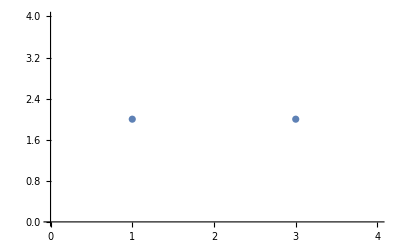

```mathematica
listData=MapThread[PopupWindow,{{{1,2},{3,2}},Map[Image,images[[234;;235]]]}]
ListPlot[listData,PlotRange->{{0,4},{0,4}}]
```